```mathematica
Clear["Global`*"]
Needs["ToMatlab`"]
y[t_] = {x1[t],x2[t],x3[t],x4[t], x5[t], x6[t]};
(*k1=0.02;k2=0.01;k3=0.001*)
k = {{-p,0,0,0, 0, 0},{p,-p ,0,0, 0, 0},{0 ,p,-p,0, 0, 0},{0 ,0,p,-p, 0, 0}, {0 ,0,0,p, -p, 0}, {0 ,0,0,0, p, 0}};
eqn = {y'[t]==k.y[t],x1[0]==1,x2[0]==0,x3[0]==0,x4[0]==0, x5[0]==0, x6[0]==0};
(*DSolve[eqn,y[t],t]*)

{x1ans[t_],x2ans[t_],x3ans[t_],x4ans[t_], x5ans[t_], x6ans[t_]}=ExpandAll[y[t]/.Flatten[DSolve[eqn,y[t],t]]];
```

Needs::nocont: Context ToMatlab` was not created when Needs was evaluated.

```mathematica
ToMatlab[FullSimplify[x6ans[t]]]
```

1+(1/24).*exp(1).^((-1).*p.*t).*((-24)+(-1).*p.*t.*(24+p.*t.*(12+ ...
  p.*t.*(4+p.*t))));

```mathematica
Simplify[x6ans[t]]
```

1/24 ⅇ^(-p t) (-24+24 ⅇ^(p t)-24 p t-12 p^2 t^2-4 p^3 t^3-p^4 t^4)

```mathematica
f[p_,t_]:=1+1/24 ⅇ^(-p t) (-24-p t (24+p t (12+p t (4+p t))))
```

```mathematica
Manipulate[Plot[f[p, t], {t, 0, 10}], {p, 1, 10}]
```

```mathematica
FullSimplify[R*( (d/kd) / (1 + d/kd) ) *( 1/24 ⅇ^(-p t) (-24+24 ⅇ^(p t)-24 p t-12 p^2 t^2-4 p^3 t^3-p^4 t^4) ) /. p-> c*d]
```

-(d ⅇ^(-c d t) R (24-24 ⅇ^(c d t)+c d t (24+c d t (12+c d t (4+c d t)))))/(24 (d+kd))

```mathematica
dmRNAdt[d_, t_, kd_, c_, R_] := -(d ⅇ^(-c d t) R (24-24 ⅇ^(c d t)+c d t (24+c d t (12+c d t (4+c d t)))))/(24 (d+kd))
```

```mathematica
-(d ⅇ^(-c d t) R (24-24 ⅇ^(c d t)+c d t (24+c d t (12+c d t (4+c d t)))))/(24 (d+kd)) //ToMatlab
```

(-1/24).*d.*exp(1).^((-1).*c.*d.*t).*(d+kd).^(-1).*R.*(24+(-24).* ...
  exp(1).^(c.*d.*t)+c.*d.*t.*(24+c.*d.*t.*(12+c.*d.*t.*(4+c.*d.*t))) ...
  );

```mathematica
ToMatlab[FullSimplify[Integrate[-(d ⅇ^(-c d t) R (24-24 ⅇ^(c d t)+c d t (24+c d t (12+c d t (4+c d t)))))/(24 (d+kd)), t]]]
```

(1/24).*c.^(-1).*exp(1).^((-1).*c.*d.*t).*(d+kd).^(-1).*R.*(120+ ...
  c.*d.*t.*(96+24.*exp(1).^(c.*d.*t)+c.*d.*t.*(36+c.*d.*t.*(8+c.*d.* ...
  t))));

```mathematica
FPT1[c_, d_] = GammaDistribution[5,1/(c*d)]
```

GammaDistribution[5,1/(c d)]

```mathematica
FPTpdf[c_,d_,t_] = PDF[FPT1[c,d],t]
```

Piecewise[{{1/24 c^5 d^5 ⅇ^(-c d t) t^4, t>0}, {0, True}}]

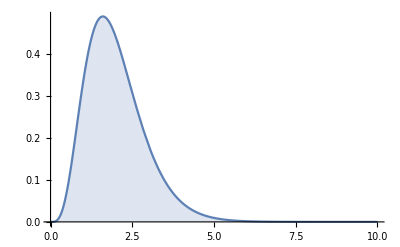

```mathematica
Plot[FPTpdf[c,d,t]/. {c->.005, d->500},{t,0,10},Filling->Axis]
```

```mathematica
Expectation[t,t\[Distributed]FPT1[c,d]]
```

5/(c d)

```mathematica
FullSimplify[Expectation[t\[Conditioned]t>10,t\[Distributed]FPT1[c,d]]] //ToMatlab
```

c.^(-1).*d.^(-1).*(3+10.*c.*d.*(3+5.*c.*d.*(3+5.*c.*d.*(2+5.*c.*d) ...
  ))).^(-1).*(15+50.*c.*d.*(3+5.*c.*d.*(3+5.*c.*d.*(2+5.*c.*d.*(1+ ...
  2.*c.*d)))));

```mathematica
FPT2[c_, d_, kd_] = GammaDistribution[5,1/(c*(d/kd) / (1 + d/kd))]
```

GammaDistribution[5,((1+d/kd) kd)/(c d)]

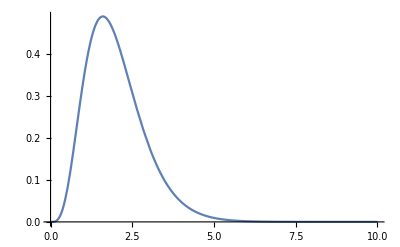

```mathematica
Plot[PDF[FPT2[c,d, kd],t] /. {c->5, d->500, kd->500}, {t, 0, 10}]
```

```mathematica
FullSimplify[FunctionExpand[Expectation[t\[Conditioned]t<10,t\[Distributed]FPT2[c,d,kd]]]] //ToMatlab
```

5.*c.^(-1).*(1+d.^(-1).*kd+2500.*c.^5.*d.^4.*(3.*d.^4+30.*c.*d.^4+ ...
  150.*c.^2.*d.^4+500.*c.^3.*d.^4+1250.*c.^4.*d.^4+12.*d.^3.*kd+90.* ...
  c.*d.^3.*kd+300.*c.^2.*d.^3.*kd+500.*c.^3.*d.^3.*kd+18.*d.^2.* ...
  kd.^2+90.*c.*d.^2.*kd.^2+150.*c.^2.*d.^2.*kd.^2+12.*d.*kd.^3+30.* ...
  c.*d.*kd.^3+3.*kd.^4+(-3).*exp(1).^(10.*c.*d.*(d+kd).^(-1)).*(d+ ...
  kd).^4).^(-1));

TF Driven with π proportional to occupancy

```mathematica
ToMatlab[FullSimplify[R*( (d/kd) / (1 + d/kd) ) *( 1/24 ⅇ^(-p t) (-24+24 ⅇ^(p t)-24 p t-12 p^2 t^2-4 p^3 t^3-p^4 t^4) ) /. p-> (c*(d/kd) / (1 + d/kd))]]
```

(1/24).*d.*exp(1).^((-1).*c.*d.*(d+kd).^(-1).*t).*(d+kd).^(-1).* ...
  R.*((-24)+24.*exp(1).^(c.*d.*(d+kd).^(-1).*t)+c.*d.*(d+kd).^(-4).* ...
  t.*((-24).*(d+kd).^3+(-12).*c.*d.*(d+kd).^2.*t+(-4).*c.^2.*d.^2.*( ...
  d+kd).*t.^2+(-1).*c.^3.*d.^3.*t.^3));

```mathematica
FullSimplify[Integrate[R*( (d/kd) / (1 + d/kd) ) *( 1/24 ⅇ^(-p t) (-24+24 ⅇ^(p t)-24 p t-12 p^2 t^2-4 p^3 t^3-p^4 t^4) ) /. p-> (c*(d/kd) / (1 + (d/kd))), t]]
```

(d R (24 t+ⅇ^(-(c d t)/(d+kd)) ((120 (d+kd))/(c d)+96 t+(36 c d t^2)/(d+kd)+(8 c^2 d^2 t^3)/(d+kd)^2+(c^3 d^3 t^4)/(d+kd)^3)))/(24 (d+kd))

```mathematica
FullSimplify[x6ans[t] /. p-> (c*(d/kd) / (1 + d/kd))] // ToMatlab
```

(1/24).*exp(1).^((-1).*c.*d.*(d+kd).^(-1).*t).*(d+kd).^(-4).*(24.* ...
  ((-1)+exp(1).^(c.*d.*(d+kd).^(-1).*t)).*kd.^4+24.*d.*kd.^3.*((-4)+ ...
  4.*exp(1).^(c.*d.*(d+kd).^(-1).*t)+(-1).*c.*t)+12.*d.^2.*kd.^2.*(( ...
  -12)+12.*exp(1).^(c.*d.*(d+kd).^(-1).*t)+(-1).*c.*t.*(6+c.*t))+4.* ...
  d.^3.*kd.*((-24)+24.*exp(1).^(c.*d.*(d+kd).^(-1).*t)+(-1).*c.*t.*( ...
  18+c.*t.*(6+c.*t)))+d.^4.*((-24)+24.*exp(1).^(c.*d.*(d+kd).^(-1).* ...
  t)+(-1).*c.*t.*(24+c.*t.*(12+c.*t.*(4+c.*t)))));